#### gr. 1

Zad. 1

```mathematica
(3+2I)/(1+2I)- I^75
(z-2)(z-1-I)(z-1+I)//Expand
Solve[%==0,z]
```

7/5+ⅈ/5

-4+6 z-4 z^2+z^3

{{z→1-ⅈ},{z→1+ⅈ},{z→2}}

Zad. 2

```mathematica
f=4 x^3-2/x^3+1/Sqrt[x];
g=Tan[x]/ArcSin[x];
h=x ArcTan[x^3];
D[f,x]//Simplify
D[g,x]
D[h,x]//Simplify
```

6/x^4-1/(2 x^(3/2))+12 x^2

Sec[x]^2/ArcSin[x]-Tan[x]/(√(1-x^2) ArcSin[x]^2)

(3 x^3)/(1+x^6)+ArcTan[x^3]

Zad. 3

-36 x-6 x^2+4 x^3+x^4

-36-12 x+12 x^2+4 x^3

{{x→-3},{x→-√3},{x→√3}}

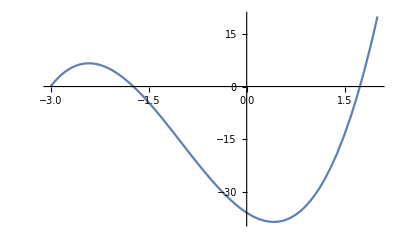

```mathematica
(x+3)(x^2-3)//Expand;
4Integrate[%,x]//Expand
D[%,x]
Solve[%==0,x]
Plot[%%,{x,-3,2}]
```

Zad. 4

```mathematica
Integrate[3/(x^2+1)-5/x^4+10/x,x]
Integrate[x (1-x^2)^7,x]
Integrate[x Sin[4x],x]
```

5/(3 x^3)+3 ArcTan[x]+10 Log[x]

-1/16 (-1+x^2)^8

-1/4 x Cos[4 x]+1/16 Sin[4 x]

Zad. 5

-3-2 x+x^2

{{x→-1},{x→3}}

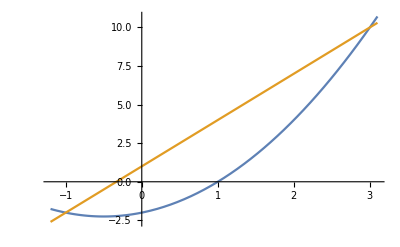

32/3

```mathematica
(x-3)(x+1)//Expand
y1=x^2+x-2;
y2=3x+1;
Solve[y1==y2,x]
Plot[{y1,y2},{x,-1.2,3.1}]
Integrate[y2-y1,{x,-1,3}]
```

Zad. 6

```mathematica
z=x^2-x y^2+y^2-x;
D[z,x]
D[z,y]
pk=Solve[{D[z,x]==0,D[z,y]==0},{x,y}]
H=Det[{{D[z,x,x],D[z,x,y]},{D[z,x,y],D[z,y,y]}}];
H/.pk
D[z,x,x]/.pk
```

-1+2 x-y^2

2 y-2 x y

{{x→1,y→-1},{x→1/2,y→0},{x→1,y→1}}

{-4,2,-4}

{2,2,2}

#### gr. 2

Zad. 1

```mathematica
(* (a) *)
x/(x+2)^2//Apart
Sqrt[%]

(* (b) *)
y=(1+x^2)/(x-3);
Limit[y,x->3,Direction->1]
Limit[y,x->3,Direction->-1]
a=Limit[y/x,x->Infinity]
b=Limit[y-a x,x->Infinity]
```

-2/(2+x)^2+1/(2+x)

√(-2/(2+x)^2+1/(2+x))

-∞

∞

1

3

Zad. 2

```mathematica
f=x^5-4/x^5+4/x^(1/4);
g=10^x/Sin[x];
h=x Log[x^2+1];
D[f,x]//Simplify
D[g,x]//Simplify
D[h,x]//Simplify
```

20/x^6-1/x^(5/4)+5 x^4

-10^x Csc[x] (Cot[x]-Log[10])

(2 x^2)/(1+x^2)+Log[1+x^2]

Zad. 3

(5+4 x-x^2)/((5+x^2)^2)

{{x→-1},{x→5}}

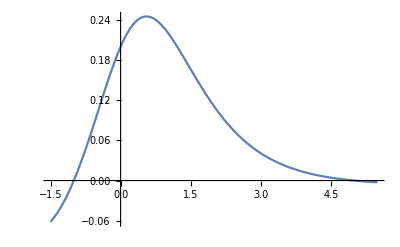

```mathematica
(x-2)/(x^2+5)//Expand;
D[%,x]//Together
Solve[%==0,x]
Plot[%%,{x,-1.5,5.5}]
```

Zad. 4

```mathematica
Integrate[1/Cos[x]^2-4/x^5+(x^2)^(1/3),x]
Integrate[1/(x Sqrt[1+Log[x]]),x]
Integrate[Log[x]/x^2,x]
```

1/x^4+3/5 x (x^2)^(1/3)+Tan[x]

2 √(1+Log[x])

-1/x-Log[x]/x

Zad. 5

-2-x+x^2

{{x→-1},{x→2}}

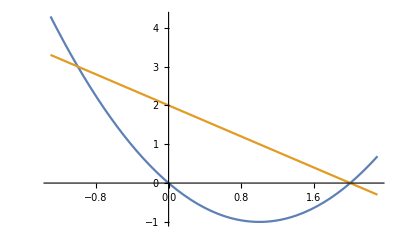

9/2

```mathematica
(x+1)(x-2)//Expand
y1=x^2-2x;
y2=-x+2;
Solve[y1==y2,x]
Plot[{y1,y2},{x,-1.3,2.3}]
Integrate[y2-y1,{x,-1,2}]
```

Zad. 6

```mathematica
z=x^3-x y+y^2-x+y;
D[z,x]
D[z,y]
pk=Solve[{D[z,x]==0,D[z,y]==0},{x,y}]
H=Det[{{D[z,x,x],D[z,x,y]},{D[z,x,y],D[z,y,y]}}];
H/.pk
D[z,x,x]/.pk
```

-1+3 x^2-y

1-x+2 y

{{x→-1/3,y→-2/3},{x→1/2,y→-1/4}}

{-5,5}

{-2,3}